3/19/22  Notebook for calculation of the stored field momentum of a positively charged, hollow sphere Q with two parallel, z directed wires in the xz plane.  The first calculation approach is to find A due to the wires, from which P = QA(r, t).  The second approach is to integrate the momentum density of the fields.

```mathematica
ClearAll["Global`*"]
mu0 = 4 * π * 10^-7;
eps0 = 8.854188 10^-12;
speedOfLight = 2.99792 10^8;
a = 5.0 10^-4;
rWire = a;
dWire = 20. rWire;     (*  Distance between the two wires  *)
current = 100.0;
q1 = 2.0 10^-12;
```

We will look at values of hField on the positive y-axis.  currentEnclosed will exclude the points inside the hollow current carrying wire, and is only needed for the top wire here, as the bottom wire is at x = -dWire/2.    hFieldX2 is always negative for x  > 0 on the x-Axis.  However, for hFieldY1, for x > 0 but less than dWire/2- rWire, it is negative, then zero inside the wire, then positive for x > dWire/2 + rWire.

```mathematica
hFieldY1[x_]:=If[Norm[x-dWire/2] > rWire, Sign[x-dWire/2.] current/(2 Pi Abs[x-dWire/2.]), 0.] ;
hFieldY2[x_]:= -current/(2 Pi (x+dWire/2.))  ;  
hFieldYTotal[x_] := hFieldY1[x] +hFieldY2[x];
```

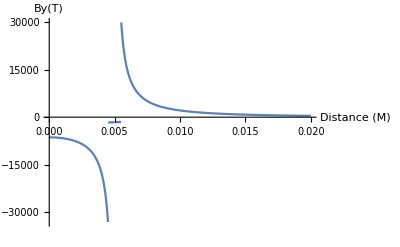

```mathematica
Plot[{hFieldYTotal[x]}, {x, 0., 40.a}, PlotRange->All, AxesLabel -> {"Distance (M)", "By(T)"}]
```

```mathematica
AofX[x_] = -Integrate[mu0 hFieldYTotal[xTemp], {xTemp, 0, x}]
```

-∫_0^x (π (-15.9155/(0.005+xTemp)+If[Norm[-0.005+xTemp]>0.0005,(Sign[xTemp-dWire/2.] current)/(2 π Abs[xTemp-dWire/2.]),0.]))/2500000 ⅆxTemp

```mathematica
numTableElements = 150;
deltaX = 1.5 dWire/(numTableElements)
xTable  = Table[dWire/2. +rWire +  (i-1)deltaX, {i, 1, numTableElements-4}]
AofXTable = Table[0.0, {i, numTableElements-4}];
```

0.0001

{0.0055,0.0056,0.0057,0.0058,0.0059,0.006,0.0061,0.0062,0.0063,0.0064,0.0065,0.0066,0.0067,0.0068,0.0069,0.007,0.0071,0.0072,0.0073,0.0074,0.0075,0.0076,0.0077,0.0078,0.0079,0.008,0.0081,0.0082,0.0083,0.0084,0.0085,0.0086,0.0087,0.0088,0.0089,0.009,0.0091,0.0092,0.0093,0.0094,0.0095,0.0096,0.0097,0.0098,0.0099,0.01,0.0101,0.0102,0.0103,0.0104,0.0105,0.0106,0.0107,0.0108,0.0109,0.011,0.0111,0.0112,0.0113,0.0114,0.0115,0.0116,0.0117,0.0118,0.0119,0.012,0.0121,0.0122,0.0123,0.0124,0.0125,0.0126,0.0127,0.0128,0.0129,0.013,0.0131,0.0132,0.0133,0.0134,0.0135,0.0136,0.0137,0.0138,0.0139,0.014,0.0141,0.0142,0.0143,0.0144,0.0145,0.0146,0.0147,0.0148,0.0149,0.015,0.0151,0.0152,0.0153,0.0154,0.0155,0.0156,0.0157,0.0158,0.0159,0.016,0.0161,0.0162,0.0163,0.0164,0.0165,0.0166,0.0167,0.0168,0.0169,0.017,0.0171,0.0172,0.0173,0.0174,0.0175,0.0176,0.0177,0.0178,0.0179,0.018,0.0181,0.0182,0.0183,0.0184,0.0185,0.0186,0.0187,0.0188,0.0189,0.019,0.0191,0.0192,0.0193,0.0194,0.0195,0.0196,0.0197,0.0198,0.0199,0.02}

```mathematica
Do[ {
x= xTable[[n]];
AofXTable[[n]] = AofX[x];
If[Mod[n, 1] == 0, 
Print[n, "   ",x, "   ",q1  AofXTable[[n]]  ]  ]
},
{n,1, numTableElements-4}]
```

1   0.0055   1.21781×10^-16

2   0.0056   1.14867×10^-16

3   0.0057   1.09077×10^-16

4   0.0058   1.04108×10^-16

5   0.0059   9.97649×10^-17

6   0.006   9.59158×10^-17

7   0.0061   9.24654×10^-17

8   0.0062   8.93437×10^-17

9   0.0063   8.64975×10^-17

10   0.0064   8.38856×10^-17

11   0.0065   8.14753×10^-17

12   0.0066   7.92401×10^-17

13   0.0067   7.71584×10^-17

14   0.0068   7.52125×10^-17

15   0.0069   7.33874×10^-17

16   0.007   7.16704×10^-17

17   0.0071   7.00507×10^-17

18   0.0072   6.85191×10^-17

19   0.0073   6.70676×10^-17

20   0.0074   6.56891×10^-17

21   0.0075   6.43775×10^-17

22   0.0076   6.31274×10^-17

23   0.0077   6.1934×10^-17

24   0.0078   6.0793×10^-17

25   0.0079   5.97007×10^-17

26   0.008   5.86535×10^-17

27   0.0081   5.76484×10^-17

28   0.0082   5.66826×10^-17

29   0.0083   5.57537×10^-17

30   0.0084   5.48592×10^-17

31   0.0085   5.39971×10^-17

32   0.0086   5.31654×10^-17

33   0.0087   5.23625×10^-17

34   0.0088   5.15867×10^-17

35   0.0089   5.08365×10^-17

36   0.009   5.01105×10^-17

37   0.0091   4.94075×10^-17

38   0.0092   4.87263×10^-17

39   0.0093   4.80658×10^-17

40   0.0094   4.74249×10^-17

41   0.0095   4.68029×10^-17

42   0.0096   4.61986×10^-17

43   0.0097   4.56114×10^-17

44   0.0098   4.50405×10^-17

45   0.0099   4.4485×10^-17

46   0.01   4.39445×10^-17

47   0.0101   4.34182×10^-17

48   0.0102   4.29055×10^-17

49   0.0103   4.24058×10^-17

50   0.0104   4.19187×10^-17

51   0.0105   4.14437×10^-17

52   0.0106   4.09802×10^-17

53   0.0107   4.05278×10^-17

54   0.0108   4.00861×10^-17

55   0.0109   3.96547×10^-17

56   0.011   3.92332×10^-17

57   0.0111   3.88212×10^-17

58   0.0112   3.84185×10^-17

59   0.0113   3.80246×10^-17

60   0.0114   3.76393×10^-17

61   0.0115   3.72623×10^-17

62   0.0116   3.68933×10^-17

63   0.0117   3.6532×10^-17

64   0.0118   3.61783×10^-17

65   0.0119   3.58317×10^-17

66   0.012   3.54921×10^-17

67   0.0121   3.51593×10^-17

68   0.0122   3.48331×10^-17

69   0.0123   3.45133×10^-17

70   0.0124   3.41996×10^-17

71   0.0125   3.38919×10^-17

72   0.0126   3.359×10^-17

73   0.0127   3.32938×10^-17

74   0.0128   3.3003×10^-17

75   0.0129   3.27175×10^-17

76   0.013   3.24372×10^-17

77   0.0131   3.21619×10^-17

78   0.0132   3.18915×10^-17

79   0.0133   3.16258×10^-17

80   0.0134   3.13648×10^-17

81   0.0135   3.11082×10^-17

82   0.0136   3.0856×10^-17

83   0.0137   3.0608×10^-17

84   0.0138   3.03642×10^-17

85   0.0139   3.01244×10^-17

86   0.014   2.98886×10^-17

87   0.0141   2.96566×10^-17

88   0.0142   2.94283×10^-17

89   0.0143   2.92036×10^-17

90   0.0144   2.89825×10^-17

91   0.0145   2.87649×10^-17

92   0.0146   2.85507×10^-17

93   0.0147   2.83397×10^-17

94   0.0148   2.8132×10^-17

95   0.0149   2.79274×10^-17

96   0.015   2.77259×10^-17

97   0.0151   2.75274×10^-17

98   0.0152   2.73318×10^-17

99   0.0153   2.71391×10^-17

100   0.0154   2.69492×10^-17

101   0.0155   2.6762×10^-17

102   0.0156   2.65775×10^-17

103   0.0157   2.63956×10^-17

104   0.0158   2.62163×10^-17

105   0.0159   2.60395×10^-17

106   0.016   2.58651×10^-17

107   0.0161   2.56931×10^-17

108   0.0162   2.55235×10^-17

109   0.0163   2.53562×10^-17

110   0.0164   2.51911×10^-17

111   0.0165   2.50282×10^-17

112   0.0166   2.48675×10^-17

113   0.0167   2.47089×10^-17

114   0.0168   2.45524×10^-17

115   0.0169   2.43979×10^-17

116   0.017   2.42454×10^-17

117   0.0171   2.40949×10^-17

118   0.0172   2.39463×10^-17

119   0.0173   2.37995×10^-17

120   0.0174   2.36546×10^-17

121   0.0175   2.35115×10^-17

122   0.0176   2.33701×10^-17

123   0.0177   2.32305×10^-17

124   0.0178   2.30926×10^-17

125   0.0179   2.29564×10^-17

126   0.018   2.28218×10^-17

127   0.0181   2.26888×10^-17

128   0.0182   2.25574×10^-17

129   0.0183   2.24276×10^-17

130   0.0184   2.22993×10^-17

131   0.0185   2.21724×10^-17

132   0.0186   2.20471×10^-17

133   0.0187   2.19232×10^-17

134   0.0188   2.18007×10^-17

135   0.0189   2.16796×10^-17

136   0.019   2.15599×10^-17

137   0.0191   2.14415×10^-17

138   0.0192   2.13244×10^-17

139   0.0193   2.12087×10^-17

140   0.0194   2.10942×10^-17

141   0.0195   2.0981×10^-17

142   0.0196   2.0869×10^-17

143   0.0197   2.07582×10^-17

144   0.0198   2.06487×10^-17

145   0.0199   2.05403×10^-17

146   0.02   2.0433×10^-17

```mathematica
ylabel="(TraditionalForm`P)_z   (kg m/s x 10^-17)"
```

(TraditionalForm`P)_z   (kg m/s x 10^-17)

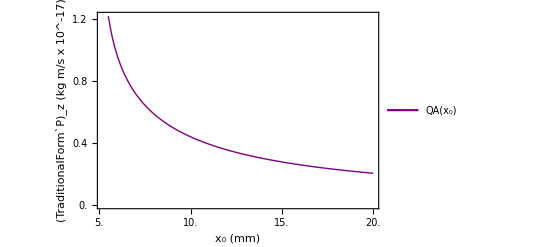

```mathematica
PCalculatedOfXList = Transpose[{xTable,q1 AofXTable}];
Plot1 = ListLinePlot[PCalculatedOfXList, FrameLabel -> {"x_0 (mm)", ylabel},  Frame -> True, FrameTicks->  {    {{#,10^16 #}&/@FindDivisions[{0. 10^-17,1.2 10^-16},6] //N,Automatic},{{#,1000 #}&/@FindDivisions[{0.005,.02},5] //N,Automatic}   } , LabelStyle->Directive[Black, FontSize -> 16], PlotLegends->Placed[{"QA(x_0)"},{Right, Center}], PlotStyle-> {Purple, Thick}, ImageMargins->{{5,5},{10,5}} ]
```

```mathematica
pIntAllSpace = {{0.0004,6.4137254676808925*^-18},{0.0008,1.291097487333625*^-17},{0.0012000000000000001,1.9581988441071326*^-17},{0.0016,2.6531849216443608*^-17},{0.002,3.3892017272509187*^-17},{0.0024000000000000002,4.183886918182287*^-17},{0.0028,5.0626808577780156*^-17},{0.0032,6.065408365030876*^-17},{0.0036000000000000003,7.261181903111828*^-17},{0.004,8.788924982375955*^-17},{0.0044,1.1006174654174424*^-16},{0.0048000000000000004,1.1902154386566437*^-16},{0.005200000000000001,1.2062176210261066*^-16},{0.0056,1.1486753360131358*^-16},{0.006,9.591610200303279*^-17},{0.0064,8.388589933141203*^-17},{0.0068000000000000005,7.521274292152748*^-17},{0.007200000000000001,6.851935160020484*^-17},{0.0076,6.312760633939217*^-17},{0.008,5.865366075614854*^-17},{0.008400000000000001,5.4859337502549896*^-17},{0.0088,5.1586857574927946*^-17},{0.0092,4.872644544952785*^-17},{0.009600000000000001,4.619874921438717*^-17},{0.01,4.3944624911439995*^-17},{0.010400000000000001,4.191886945083837*^-17},{0.0108,4.008620255425377*^-17},{0.0112,3.841859460162863*^-17},{0.011600000000000001,3.6893433818753916*^-17},{0.012,3.5492235513189964*^-17},{0.012400000000000001,3.4199712030977784*^-17},{0.0128,3.3003089103118564*^-17},{0.0132,3.189159437832968*^-17},{0.013600000000000001,3.0856068741511625*^-17},{0.014,2.988866678043723*^-17},{0.014400000000000001,2.898262302923134*^-17},{0.0148,2.813206745721532*^-17},{0.0152,2.733187831253081*^-17},{0.015600000000000001,2.6577563645714477*^-17},{0.016,2.586516509358444*^-17},{0.0164,2.5191179116277516*^-17},{0.016800000000000002,2.4552492045783564*^-17},{0.0172,2.3946326158787738*^-17},{0.0176,2.3370194617584318*^-17},{0.018000000000000002,2.2821863599348513*^-17},{0.0184,2.2299320291071397*^-17},{0.0188,2.1800745702284715*^-17},{0.019200000000000002,2.1324491458576524*^-17},{0.0196,2.086905990317455*^-17},{0.02,2.0433086961741862*^-17}}
```

{{0.0004,6.41373×10^-18},{0.0008,1.2911×10^-17},{0.0012,1.9582×10^-17},{0.0016,2.65318×10^-17},{0.002,3.3892×10^-17},{0.0024,4.18389×10^-17},{0.0028,5.06268×10^-17},{0.0032,6.06541×10^-17},{0.0036,7.26118×10^-17},{0.004,8.78892×10^-17},{0.0044,1.10062×10^-16},{0.0048,1.19022×10^-16},{0.0052,1.20622×10^-16},{0.0056,1.14868×10^-16},{0.006,9.59161×10^-17},{0.0064,8.38859×10^-17},{0.0068,7.52127×10^-17},{0.0072,6.85194×10^-17},{0.0076,6.31276×10^-17},{0.008,5.86537×10^-17},{0.0084,5.48593×10^-17},{0.0088,5.15869×10^-17},{0.0092,4.87264×10^-17},{0.0096,4.61987×10^-17},{0.01,4.39446×10^-17},{0.0104,4.19189×10^-17},{0.0108,4.00862×10^-17},{0.0112,3.84186×10^-17},{0.0116,3.68934×10^-17},{0.012,3.54922×10^-17},{0.0124,3.41997×10^-17},{0.0128,3.30031×10^-17},{0.0132,3.18916×10^-17},{0.0136,3.08561×10^-17},{0.014,2.98887×10^-17},{0.0144,2.89826×10^-17},{0.0148,2.81321×10^-17},{0.0152,2.73319×10^-17},{0.0156,2.65776×10^-17},{0.016,2.58652×10^-17},{0.0164,2.51912×10^-17},{0.0168,2.45525×10^-17},{0.0172,2.39463×10^-17},{0.0176,2.33702×10^-17},{0.018,2.28219×10^-17},{0.0184,2.22993×10^-17},{0.0188,2.18007×10^-17},{0.0192,2.13245×10^-17},{0.0196,2.08691×10^-17},{0.02,2.04331×10^-17}}

```mathematica
pIntAllSpaceA = {{0.0056,1.1486753360131358*^-16},{0.006,9.591610200303279*^-17},{0.0064,8.388589933141203*^-17},{0.0068000000000000005,7.521274292152748*^-17},{0.007200000000000001,6.851935160020484*^-17},{0.0076,6.312760633939217*^-17},{0.008,5.865366075614854*^-17},{0.008400000000000001,5.4859337502549896*^-17},{0.0088,5.1586857574927946*^-17},{0.0092,4.872644544952785*^-17},{0.009600000000000001,4.619874921438717*^-17},{0.01,4.3944624911439995*^-17},{0.010400000000000001,4.191886945083837*^-17},{0.0108,4.008620255425377*^-17},{0.0112,3.841859460162863*^-17},{0.011600000000000001,3.6893433818753916*^-17},{0.012,3.5492235513189964*^-17},{0.012400000000000001,3.4199712030977784*^-17},{0.0128,3.3003089103118564*^-17},{0.0132,3.189159437832968*^-17},{0.013600000000000001,3.0856068741511625*^-17},{0.014,2.988866678043723*^-17},{0.014400000000000001,2.898262302923134*^-17},{0.0148,2.813206745721532*^-17},{0.0152,2.733187831253081*^-17},{0.015600000000000001,2.6577563645714477*^-17},{0.016,2.586516509358444*^-17},{0.0164,2.5191179116277516*^-17},{0.016800000000000002,2.4552492045783564*^-17},{0.0172,2.3946326158787738*^-17},{0.0176,2.3370194617584318*^-17},{0.018000000000000002,2.2821863599348513*^-17},{0.0184,2.2299320291071397*^-17},{0.0188,2.1800745702284715*^-17},{0.019200000000000002,2.1324491458576524*^-17},{0.0196,2.086905990317455*^-17},{0.02,2.0433086961741862*^-17}}
```

{{0.0056,1.14868×10^-16},{0.006,9.59161×10^-17},{0.0064,8.38859×10^-17},{0.0068,7.52127×10^-17},{0.0072,6.85194×10^-17},{0.0076,6.31276×10^-17},{0.008,5.86537×10^-17},{0.0084,5.48593×10^-17},{0.0088,5.15869×10^-17},{0.0092,4.87264×10^-17},{0.0096,4.61987×10^-17},{0.01,4.39446×10^-17},{0.0104,4.19189×10^-17},{0.0108,4.00862×10^-17},{0.0112,3.84186×10^-17},{0.0116,3.68934×10^-17},{0.012,3.54922×10^-17},{0.0124,3.41997×10^-17},{0.0128,3.30031×10^-17},{0.0132,3.18916×10^-17},{0.0136,3.08561×10^-17},{0.014,2.98887×10^-17},{0.0144,2.89826×10^-17},{0.0148,2.81321×10^-17},{0.0152,2.73319×10^-17},{0.0156,2.65776×10^-17},{0.016,2.58652×10^-17},{0.0164,2.51912×10^-17},{0.0168,2.45525×10^-17},{0.0172,2.39463×10^-17},{0.0176,2.33702×10^-17},{0.018,2.28219×10^-17},{0.0184,2.22993×10^-17},{0.0188,2.18007×10^-17},{0.0192,2.13245×10^-17},{0.0196,2.08691×10^-17},{0.02,2.04331×10^-17}}

```mathematica
legendsp="∫ϵ_0(E x B)dv"
```

∫ϵ_0(E x B)dv

```mathematica
Plot2 = ListPlot[pIntAllSpaceA, Frame -> True, FrameTicks->  {    {{#,10^16 #}&/@FindDivisions[{0. 10^-17,1.2 10^-16},6] //N,Automatic},{{#,1000 #}&/@FindDivisions[{0.0,.02},5] //N,Automatic}   } , LabelStyle->Directive[Black, FontSize -> 14], PlotLegends->Placed[{legendsp},{Right, Center}], PlotMarkers->{"●"}, PlotStyle-> Blue]
```

-Graphics-

```mathematica
Show[Plot1, Plot2]
```

-Graphics-